2021 - 06 - 13 , some excercises from the book

```mathematica
40.1
```

```mathematica
Clear[x]
```

```mathematica
sq[t_]=t^2
```

t^2

```mathematica
sq[2]
```

4

```mathematica
poly[n_Integer]:=Graphics[Style[RegularPolygon[n],Orange]]
```

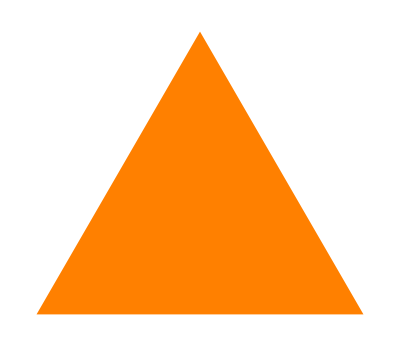
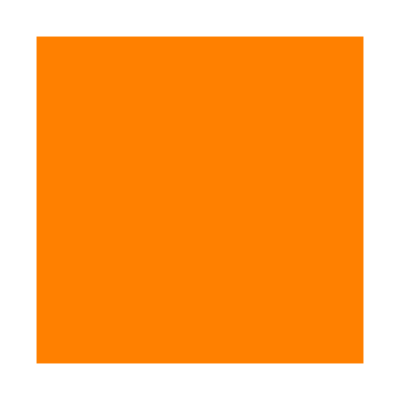
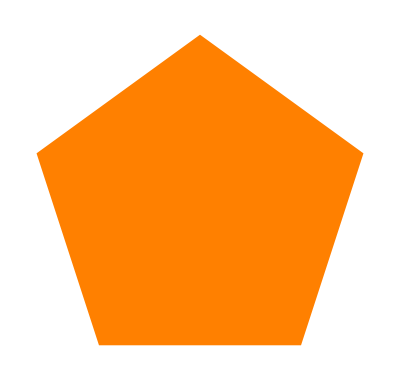
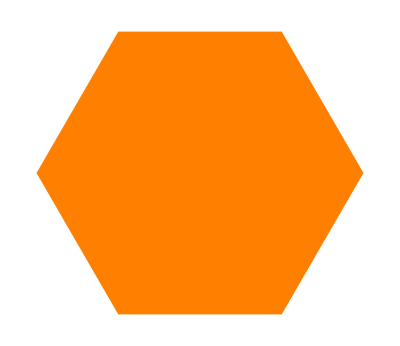
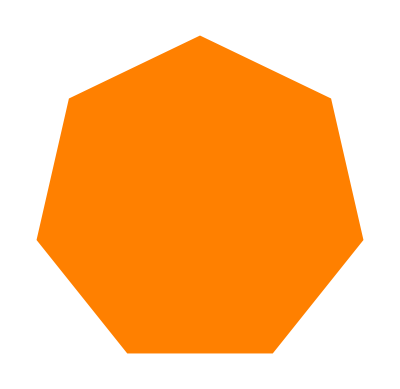
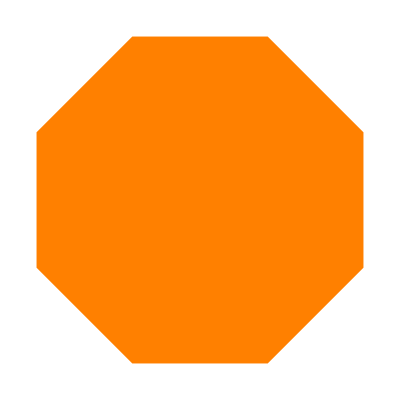
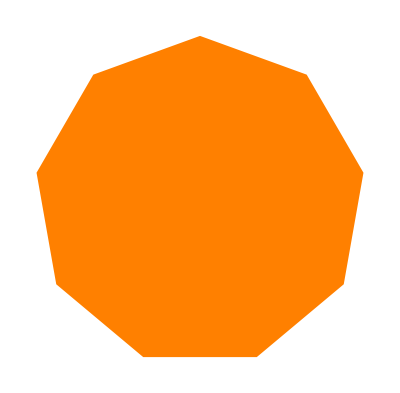
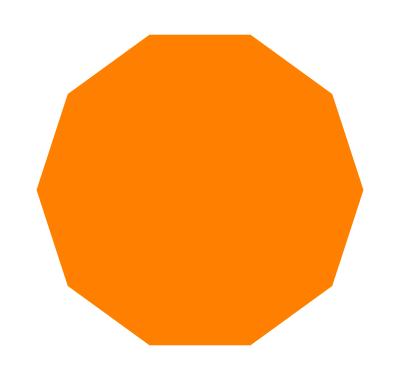

```mathematica
Table[poly[n],{n,3,10}]
```

```mathematica
Clear[f];
f[{a_,b_}] = {b,a}
```

{b,a}

```mathematica
f[{1,2}]
```

{2,1}

```mathematica
Clear[f];
f[a_,b_]:=a*b/(a+b);
```

```mathematica
f[1,10]
```

10/11

```mathematica
Clear[f];
f[{a_,b_}] ={a+b,a-b,a/b}
```

{a+b,a-b,a/b}

```mathematica
f[{1,3}]
```

{4,-2,1/3}

```mathematica
Clear[evenodd];
evenodd[0]=Red;evenodd[x_]:=If[EvenQ[x],Black,White]; Table[Column[{x,evenodd[x]}],{x,-3,3}]
```

{-3
GrayLevel[1],-2
GrayLevel[0],-1
GrayLevel[1],0
RGBColor[1, 0, 0],1
GrayLevel[1],2
GrayLevel[0],3
GrayLevel[1]}

```mathematica
If[EvenQ[2],1,0]
```

1

```mathematica
Clear[fib];
fib[0]=1;fib[1]=1;fib[n_Integer]:=fib[n-1]+fib[n-2];Table[Column[{x,fib[x]}],{x,0,10}]
```

{0
1,1
1,2
2,3
3,4
5,5
8,6
13,7
21,8
34,9
55,10
89}

```mathematica
animalImage[s_String] := Interpreter["Animal"][s]["Image"];
animalImage["Tiger"]
```

-Graphics-

```mathematica
animalImage["sealion"]
```

-Graphics-

```mathematica
animalImage["rat"]
```

-Graphics-

```mathematica
Clear[nearword];
nearword[s_String,n_Integer]:=Nearest[WordList[],s,n];
nearword[s_String]:=nearword[s,10];
```

```mathematica
nearword["test",10]
```

{test,best,jest,lest,nest,pest,rest,teat,tent,testy}

```mathematica
nearword["why",10]
```

{why,shy,thy,way,whey,who,wry,achy,ah,aha}

```mathematica
nearword["qq"]
```

{a,ad,ah,am,an,as,at,ax,be,by}

```mathematica
?nearword
```

```mathematica
?fib
```

```mathematica
fib[-10]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of fib[-1032-1].

Hold[fib[-10-1]+fib[-10-2]]

```mathematica
Clear[headpat];
headpat[x_Int]:={"I_",x};headpat[x_S_]:={"S_",x};
```

```mathematica
headpat[String[1]]
```

headpat[String[1]]

```mathematica
String["11"]
```

String[11]

```mathematica
Head["11"]
```

String

```mathematica
headpat["11"]
```

headpat[11]

```mathematica
?headpat
```

```mathematica
Clear[checkab];checkab[x_,y_]:={x,y}/;x≥y
```

```mathematica
checkab[x_,y_]:={y+1,x}/;x≤y;
```

```mathematica
checkab[3,3]
```

{3,3}

```mathematica
Clear[blackwhite]; blackwhite[{___,Black,x___,White,___}]:={Black,x,White};
```

```mathematica
blackwhite[{Red,Black,Red,Red,Black,White,White}]
```

{GrayLevel[0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],GrayLevel[0],GrayLevel[1]}

```mathematica
Graphics[%]
```

41.1 Lists of digits of squares of integers below 100 containing successice repeated digits

```mathematica
Select[Table[IntegerDigits[x^2],{x,1,100}],MatchQ[#,{___,x_,x_,___}]&]
```

{{1,0,0},{1,4,4},{2,2,5},{4,0,0},{4,4,1},{9,0,0},{1,1,5,6},{1,2,2,5},{1,4,4,4},{1,6,0,0},{2,1,1,6},{2,2,0,9},{2,5,0,0},{3,3,6,4},{3,6,0,0},{3,8,4,4},{4,2,2,5},{4,4,8,9},{4,9,0,0},{5,7,7,6},{6,4,0,0},{6,8,8,9},{7,2,2,5},{7,7,4,4},{8,1,0,0},{8,8,3,6},{1,0,0,0,0}}

```mathematica
StringJoin/@ Select[Table[Characters[RomanNumeral[x]],{x,1,100}],MatchQ[#,{___,"L",___,"I",___,"X",___}]&]
```

{XLIX,LIX,LXIX,LXXIX,LXXXIX}

```mathematica
Clear[f];
f[x_List]:=x==Reverse[x];
```

```mathematica
f[{1,2}]
```

False

```mathematica
f[{1,32,1,32,1}]
```

True

41.4

```mathematica
WikipediaData["Alliteration"]//ToLowerCase//TextWords//Partition[#,2,1]&//Select[#1,Characters[#1[[1]]][[1]]==Characters[#1[[2]]][[1]]&]&
```

{{identical,initial},{as,a},{humble,house},{potential,power},{power,play},{peter,piper},{piper,picked},{pickled,peppers},{accept,as},{as,alliteration},{to,the},{to,the},{lazy,languid},{languid,line},{at,any},{home,hot},{is,in},{stressed,syllable},{to,the},{as,alliterating},{as,anglo-saxon},{of,outside},{same,sound},{of,outside},{to,the},{brown,blazers},{colour,co-ordination},{in,its},{silken,sad},{breeze,blew},{foam,flew},{furrow,followed},{followed,free},{stood,still},{alliteration,and},{churlish,chiding},{winter’s,wind},{wind,which},{which,when},{alphabetical,africa},{chapter,consists},{abish,allows},{at,all},{vaka,vanha},{vanha,väinämöinen},{the,thistle},{written,with},{brent,bernard},{who,watch},{watch,with},{with,wild},{wild,wonder},{wide,window},{beautiful,birds},{birds,begin},{bountiful,birdseed},{grey,geese},{grey,geese},{grazing,grey},{the,tongue-twister},{betty,botter},{botter,by},{betty,botter},{botter,bought},{butter,but},{she,said},{butter's,bitter},{if,i},{it,in},{make,my},{batter,bitter},{bitter,but},{better,butter},{make,my},{bitter,batter},{batter,better},{peter,piper},{piper,peter},{peter,piper},{piper,picked},{pickled,peppers},{peter,piper},{piper,picked},{pickled,peppers},{pickled,peppers},{peppers,peter},{peter,piper},{piper,picked},{of,old},{irish,it},{important,ingredient},{sanskrit,shlokas},{æthelwulf,æthelbald},{æthelbald,æthelberht},{direct,descendants},{tancred,torhtred},{poetry,poets},{can,call},{splendid,silent},{silent,sun},{walt,whitman},{splendid,silent},{silent,sun},{wondered,what},{his,horse},{by,bernard},{r.,r.},{tolkien's,translation},{translation,this},{fact,follows},{an,alliterative},{also,add},{to,the},{harsh,hard},{they,than},{slippered,sleep},{lean,lithe},{fleet,flown},{an,artistic},{emotional,effect},{and,attention-grabbing},{s,sounds},{can,create},{any,attitude},{as,a},{adds,a},{an,audience's},{audience's,attention},{attention,and},{evokes,emotion},{is,in},{times,the},{as,an},{which,we},{our,only},{of,our},{his,help},{our,own},{but,by},{today,that},{that,the},{truths,that},{is,inextricably},{to,the},{itself,is},{testimony,to},{to,the},{have,had},{because,brave},{freedom's,front},{ronald,reagan},{vietnam,veterans},{new,nation},{to,the},{patent,portae},{portae,proficiscere},{and,adds},{adds,an},{an,alliterative},{μάρθα,μάρθα},{μάρθα,μεριμνᾷς},{martha,martha},{martha,merimnas},{martha,martha},{modern,music},{cartoon,characters},{helplessly,hoping},{by,bob},{throughout,the},{the,tonight},{copper,clapper},{clapper,caper},{also,alliteration},{anadiplosis,assonance},{house,handbook},{alliterations,and}}

```mathematica
g:=Select[#1,Characters[#1[[1]]][[1]]==Characters[#1[[2]]][[1]]&]&
```

```mathematica
g[{{"aa","aa"}}]
```

{{aa,aa}}

```mathematica
Clear[a]
```

```mathematica
A=FixedPointList[#/.{a___,x_,y_,b___}/;x>y->{a,y,x,b}&,{5,4,1,3,2}]
```

{{5,4,1,3,2},{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5}}

```mathematica
Grid[a]
```

5 | 4 | 1 | 3 | 2
4 | 5 | 1 | 3 | 2
4 | 1 | 5 | 3 | 2
1 | 4 | 5 | 3 | 2
1 | 4 | 3 | 5 | 2
1 | 3 | 4 | 5 | 2
1 | 3 | 4 | 2 | 5
1 | 3 | 2 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5

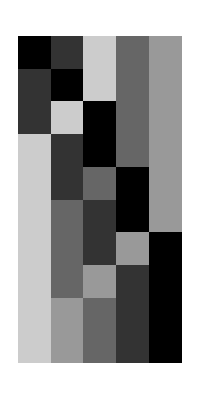

```mathematica
ArrayPlot[a]
```

```mathematica
ArrayPlot[FixedPointList[#/.{a___,x_,y_,b___}/;x>y->{a,y,x,b}&,RandomSample[Range[50],50]],AspectRatio->1]
```

-Graphics-

```mathematica
NestList[(#+2/#)/2&,1,10]// N[#,100]&
```

{1.,1.5,1.416666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667,1.414215686274509803921568627450980392156862745098039215686274509803921568627450980392156862745098039,1.41421356237468991062629557889013491011655962211574404458490501920005437183538926835899004315764434,1.414213562373095048801689623502530243614981925776197428498289498623195824228923621784941836735830357,1.414213562373095048801688724209698078569671875377234001561013133113265255630339978531787161250710475,1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641602,1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573,1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573,1.414213562373095048801688724209698078569671875376948073176679737990732478462107038850387534327641573}

```mathematica
Clear[nn];nn[x_]:=(x+2/x)/2;
```

```mathematica
nn[17/12]
```

577/408

```mathematica
Solve[x==(x+2/x)/2,{x}]
```

{{x→-√2},{x→√2}}

```mathematica
Clear[eGCD,a,b];
eGCD[{a_,b_}/;b==0]={a,b};
eGCD[{a_,b_}]={b,Mod[a,b]};
```

```mathematica
FixedPointList[eGCD,{12345,54321}]
```

{{12345,54321},{54321,12345},{12345,4941},{4941,2463},{2463,15},{15,3},{3,0},{3,0}}

```mathematica
GCD[12345,54321]
```

3

```mathematica
IntegerDigits[100!]/.{a___,b:0 ..}->{a}
```

{9,3,3,2,6,2,1,5,4,4,3,9,4,4,1,5,2,6,8,1,6,9,9,2,3,8,8,5,6,2,6,6,7,0,0,4,9,0,7,1,5,9,6,8,2,6,4,3,8,1,6,2,1,4,6,8,5,9,2,9,6,3,8,9,5,2,1,7,5,9,9,9,9,3,2,2,9,9,1,5,6,0,8,9,4,1,4,6,3,9,7,6,1,5,6,5,1,8,2,8,6,2,5,3,6,9,7,9,2,0,8,2,7,2,2,3,7,5,8,2,5,1,1,8,5,2,1,0,9,1,6,8,6,4}

```mathematica
100!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

```mathematica
{a,b}/.{a->1,b->2}
```

{1,2}

```mathematica
Clear[x,y,z,s,k];
FixedPointList[#/.{s[x_][y_][z_]->x[z][y[z]],k[x_][y_]->x}&, s[s][k][s[s[s]][s]][s]]
```

{s[s][k][s[s[s]][s]][s],s[s[s[s]][s]][k[s[s[s]][s]]][s],s[s[s]][s][s][k[s[s[s]][s]][s]],s[s][s][s[s]][s[s[s]][s]],s[s[s]][s[s[s]]][s[s[s]][s]],s[s][s[s[s]][s]][s[s[s]][s[s[s]][s]]],s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s]][s[s[s]][s]]]],s[s[s[s]][s[s[s]][s]]][s[s][s[s[s]][s[s[s]][s]]][s[s[s[s]][s[s[s]][s]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s]][s[s[s]][s]][s[s[s[s]][s[s[s]][s]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]][s[s[s[s]][s[s[s]][s]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]]}

```mathematica
FixedPointList[#/.{s[x_][y_][z_]->x[z][y[z]],k[x_][y_]->x}&, s[s][k][s[s[s]]][s]]
```

{s[s][k][s[s[s]]][s],s[s[s[s]]][k[s[s[s]]]][s],s[s[s]][s][k[s[s[s]]][s]],s[s][k[s[s[s]]][s]][s[k[s[s[s]]][s]]],s[s[k[s[s[s]]][s]]][k[s[s[s]]][s][s[k[s[s[s]]][s]]]],s[s[s[s[s]]]][s[s[s]][s[s[s[s]]]]],s[s[s[s[s]]]][s[s[s]][s[s[s[s]]]]]}

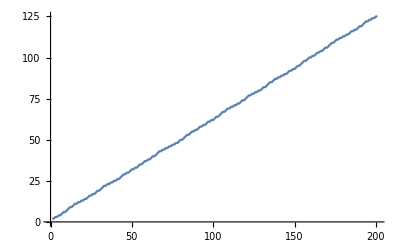

```mathematica
ListLinePlot[Length/@NestList[#/.{{1,_,a___}->{a,0,1},{0,_,a___}->{a,1,0,0}}&,{1,0},200]]
```

```mathematica
NestList[#/.{{1,_,a___}->{a,0,1},{0,_,a___}->{a,1,0,0}}&,{1,0},200]
```

{{1,0},{0,1},{1,0,0},196,{1,1,0,0,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0},{0,0,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,1,1,0,0,1,0,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1}}
 |  |  |  |

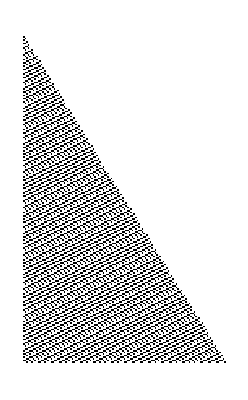

```mathematica
ArrayPlot[NestList[#/.{{1,_,a___}->{a,0,1},{0,_,a___}->{a,1,0,0}}&,{1,0},200]]
```

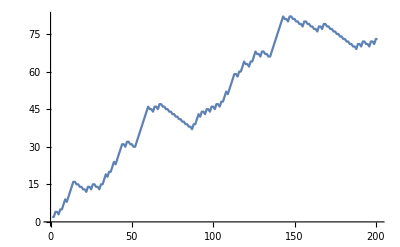

```mathematica
ListLinePlot[Length/@NestList[#/.{{2,_,a___}->{a,0,2,1,2},{1,_,a___}->{a,0},{0,_,a___}->{a,2,1}}&,{0,0},200]]
```